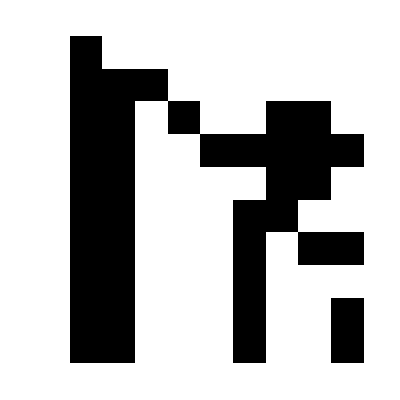
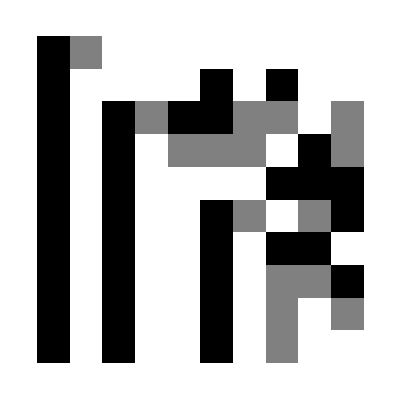
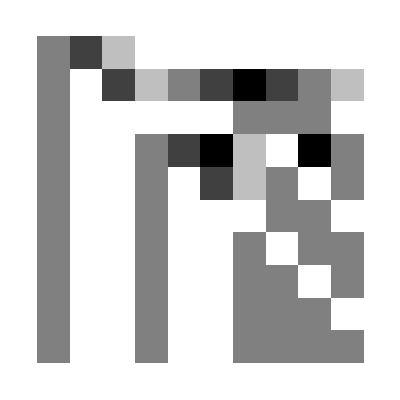

```mathematica
Table[ArrayPlot[Table[Reverse[IntegerDigits[CatalanNumber[Prime[k]^n],Prime[k],10]],{n,1,10}]],{k,1,3}]
```

```mathematica
Show[
ArrayPlot[Table[Reverse[IntegerDigits[CatalanNumber[Prime[1]^n],Prime[1],10]],{n,1,10}]],
ArrayPlot[Table[Reverse[IntegerDigits[CatalanNumber[Prime[2]^n],Prime[2],10]],{n,1,10}]],
ArrayPlot[Table[Reverse[IntegerDigits[CatalanNumber[Prime[3]^n],Prime[3],10]],{n,1,10}]]]
```

```mathematica
ArrayPlot[Table[Reverse[IntegerDigits[CatalanNumber[Prime[1]^n],Prime[1],20]],{n,1,20}]]
```

-Graphics-

```mathematica
Manipulate[Module[{F=(Fun/.n->#)&},
ArrayPlot[Table[IntegerDigits[F[n],2],{n,1,rows}],ImageSize->Large]],{Fun,n},{rows,10}]
```

```mathematica
Manipulate[Module[{Fun=(F/.n->#)&},
ArrayPlot[Table[IntegerDigits[Fun[n]-Fun[n-1],2],{n,1,rows}]]],{F,n},{rows,10}]
```

```mathematica
Valuation[n_,p_]:=Valuation[n,p]=IntegerExponent[Abs[Numerator[n]],p]-IntegerExponent[Denominator[n],p]
```

```mathematica
SetAttributes[Valuation,Listable]
```

### Automatic Sequence Guesser

```mathematica
PullSequence[F_,p_,coords_,values_]:=
(*
The function is designed to pull the subsequence of the sequence which corresponds to a given vertex of the tree
F is the function giving us the terms of a sequence
p is the number of branchings
coords is a list of the digits read to get to a certain vertex
values is the size of the list of entries of the sequence which correspond to the vertex
*)Module[{k=Length[coords],start},
start=Mod[Sum[coords[[n]]*p^(n-1),{n,1,k}],p^(k)];
Table[F[start+n*p^k],{n,0,values-1}]
]
```

```mathematica
CalcStart[seq_,p_]:=If[seq=={},0,Mod[Sum[seq[[n]]*p^(n-1),{n,1,Length[seq]}],p^(Length[seq])]]
```

```mathematica
Initialize[F_,branches_,values_]:=
(*This simplifies use of AS*)
{F,branches,values,0,{},{},{},{{}}}
```

```mathematica
AS[prev_]:=(* THE MAIN EVENT, Feast your eyes...
The function calculates the next depth of a graph representing an automatic sequence
The argument is a list of the following 8 elements:
 1: Function producing the sequence
2: number of branches
3: number of values to test for equality before considering two sequences to be equal.
Ideally you would compare infinitely many, but we don't have that option, now do we?
4:depth of graph from argument 5
 5:the graph so far, to be augmented by further calculation
 6: the list of previously encountered sequences
 7: the list of coordinates of previously encountered sequences
 8: the list of coordinates whose place in the automaton must still be determined.
	*)
Module[
{graph=prev[[5]],(*a list of coordinates paired with their corresponding outgoing edges in the form of {digit,name of target}*)
store=prev[[6]],(*list of sequences encountered already*)
names=prev[[7]],(*names of nodes corresponding to sequences seen*)
queue=prev[[8]],(*coordinates remaining to check*)
depth=0,(*length of largest coordinate -> how far down the tree goes before recursing or before the computation quits*)
coords,(*coordinates currently being checked*)
list,(*subsequence corresponding to coordinates being checked*)
name,(*name corresponding to current coordinates*)
position (*where to find the name of a node when a match is found*)
},
While[depth≤ prev[[4]] && queue≠{},
coords=queue[[1]];
name=coords;
queue=Drop[queue,1];
list=PullSequence[prev[[1]],prev[[2]],coords,prev[[3]]];
position=Position[store,list];
If[position≠{},(*thus it has been seen already*)
AppendTo[graph,{Drop[name,-1],{Last[coords],names[[position[[1,1]]]]}}],
AppendTo[store,list];
AppendTo[names,name];
queue=Join[queue,Table[Append[coords,k],{k,0,prev[[2]]-1}]];
graph=If[name=={},graph,AppendTo[graph,{Drop[name,-1],{Last[name],name}}]
];
];
depth=Max[Table[Length[queue[[n]]],{n,1,Length[queue]}]];
];
{prev[[1]],prev[[2]],prev[[3]],prev[[4]]+1,graph,store,names,queue}
]
```

### Rendering the Trees

```mathematica
MakeVertexName[list_]:=StringJoin[ToString/@Riffle[Join[{"a"},list],"_"]]
```

```mathematica
Edges[graph_]:=DeleteDuplicates[Table[MakeVertexName[graph[[n,1]]]->MakeVertexName[graph[[n,2,2]]],{n,1,Length[graph]}]]
```

```mathematica
MakeEdgeLabels[graph_]:=Module[{position,edgelabel,from,to,pair,pairs={},label,
edgelabels={},i=0},
While[i< Length[graph],
i=i+1;
from=graph[[i,1]];
to=graph[[i,2,2]];
label=graph[[i,2,1]];
pair={from,to};
position=Position[pairs,pair];
If[position≠{},
AppendTo[edgelabels[[position[[1,1]],2]],label],
AppendTo[pairs,pair];
AppendTo[edgelabels,Labeled[MakeVertexName[from]->MakeVertexName[to],{label}]];
];
];
edgelabels
]
```

```mathematica
MakeVertexLabels[graph_]:=Table[MakeVertexName[graph[[5]][[n,1]]]->graph[[1]][CalcStart[graph[[5]][[n,1]],graph[[2]]]] ,{n,1,Length[graph[[5]]]}]
```

```mathematica
M=Initialize[Valuation[CatalanNumber[3^#],3]&,3,15];
Nest[AS,M,3];
```

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

```mathematica
(*Manipulate[
Graph[MakeEdgeLabels[Nest[AS,Initialize[Valuation[CatalanNumber[p^#],p]&,p,15],4]],VertexLabels->MakeVertexLabels[graph]],{p,2}]
```

```mathematica
Manipulate[ArrayPlot[Table[Reverse[IntegerDigits[CatalanNumber[2^n+2^(n-k)],2,30]],{n,k,k+15}]],{k,0}]
```

```mathematica
ArrayPlot[Table[Last[Table[Reverse[IntegerDigits[CatalanNumber[2^n+2^(n-k)+1],2,30]],{n,k,20}]],{k,0,15}]]
```

-Graphics-

```mathematica
Table[Last[Table[Reverse[IntegerDigits[CatalanNumber[2^n+2^(n-k)+1],2,30]],{n,k,20}]],{k,0,15}]
```

{{0,1,1,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,1,0,1,0,0,0,1,1,0,0,1,1},{0,0,1,1,1,0,0,0,1,1,1,1,1,1,0,0,0,1,0,1,0,1,0,1,0,1,0,1,1,0},{0,0,1,0,1,1,0,0,1,1,1,0,0,1,1,1,0,1,0,0,1,0,0,1,0,0,0,1,0,0},{0,0,1,0,0,0,1,1,0,0,0,0,1,0,1,1,0,1,0,0,1,0,1,1,1,0,1,1,0,1},{0,0,1,0,0,1,1,0,0,0,1,0,0,1,1,0,0,1,0,1,1,0,0,1,0,0,0,0,0,0},{0,0,1,0,0,1,0,1,1,0,1,0,1,0,0,0,0,1,1,1,1,1,0,0,0,0,0,1,0,1},{0,0,1,0,0,1,0,0,0,0,0,0,0,1,1,0,0,1,1,1,1,0,0,0,1,0,1,0,0,1},{0,0,1,0,0,1,0,0,1,0,1,0,1,0,1,0,1,0,1,1,1,0,0,0,0,0,0,1,0,0},{0,0,1,0,0,1,0,0,1,1,1,1,1,0,0,0,1,0,1,0,1,0,0,1,0,1,1,1,0,0},{0,0,1,0,0,1,0,0,1,1,0,0,0,1,1,0,0,0,1,0,0,0,0,1,1,0,1,1,0,1},{0,0,1,0,0,1,0,0,1,1,0,0,0,0,1,1,1,0,1,1,1,1,0,0,0,1,0,1,1,1},{0,0,1,0,0,1,0,0,1,1,1,1,0,1,1,1,1,0,1,1,0,0,0,0,0,1,0,0,1,1},{0,0,1,0,0,1,0,0,1,0,1,1,1,1,1,1,1,0,1,1,1,1,1,0,0,1,1,0,0,0},{0,0,1,0,0,1,0,0,0,0,1,0,1,1,0,0,0,1,0,0,1,1,0,0,0,1,0,1,0,0},{0,0,1,0,0,1,0,1,1,1,1,1,1,1,0,1,1,0,1,1,1,0,1,0,1,1,1,1,1,1},{0,0,1,0,0,1,1,0,1,0,0,1,0,1,1,0,0,1,1,1,0,0,0,1,0,1,0,1,1,0}}

```mathematica
PGamma[n_,p_]:=(-1)^n*Product[If[Mod[j,p]==0,1,j],{j,1,n-1}]
```

```mathematica
Catalimit2[digits_]:=
Reverse[IntegerDigits[PolynomialMod[2Product[Product[2j+1,{j,2^i,2^(i+1)-1}]^i,{i,0,digits}],2^digits],2,digits]]
```

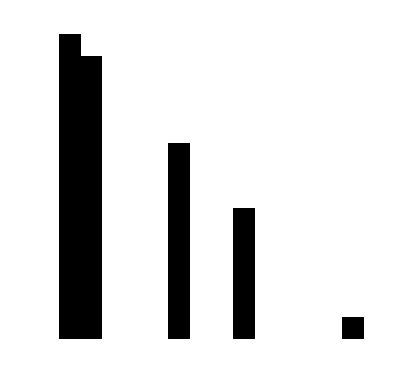

```mathematica
ArrayPlot[Table[Catalimit2[k],{k,2,15}]]
```

```mathematica
M=Catalimit2[20]
```

{0,1,1,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,1,0}

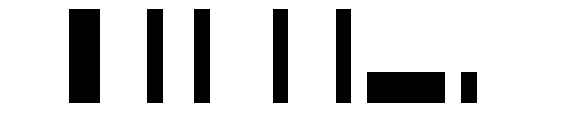
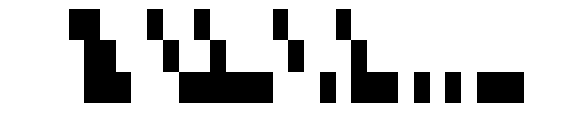
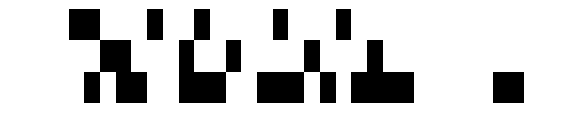
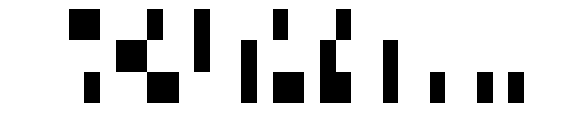

```mathematica
Table[ArrayPlot[{M,Flatten[Prepend[M,Table[0,{i,1,k}]]],Reverse[IntegerDigits[CatalanNumber[2^20+2^(20-k)],2,30]]},ImageSize->Large],{k,0,3}]
```

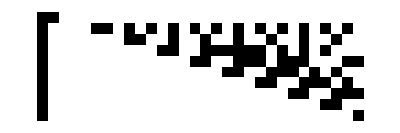

```mathematica
ArrayPlot[Table[Reverse[IntegerDigits[PolynomialMod[PGamma[2^(n+1),2]/(PGamma[2^(n)+1,2]^2),2^30],2,30]],{n,1,10}]]
```

```mathematica
Product[,{,i}]
```